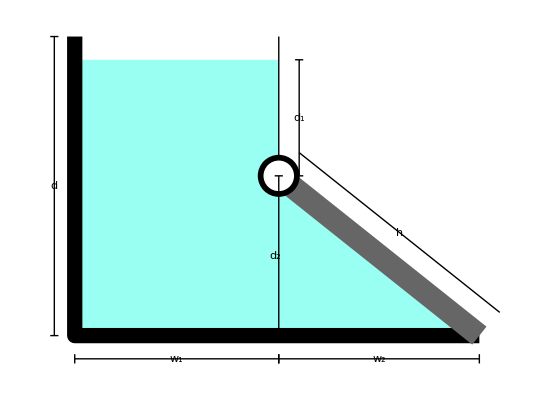

```mathematica
Module[{col,δ,h,θ,d2,w2,w1,d1,d,txt1,txt2},
col=RGBColor[0.6,1,0.95];δ=0.25;
h=3;θ=35°;d2=h*Sin[θ];w2=h*Cos[θ];
w1=2.5;d1=1.25;d=3.221;

txt1[var_]:=Framed[Style[var,17,Italic],Background->White,FrameStyle->None,FrameMargins->Tiny];
txt2[var_,sub_]:=Framed[Style[Subscript[Style[var,Italic],sub],17],Background->White,FrameStyle->None,FrameMargins->Tiny];

Graphics[{
{col,Polygon[{{w1,d1+d2},{0,d1+d2},{0,0},{w1+w2,0},{w1,d2}}]},

{Thickness@0.02,CapForm@None,Line[{{0,d},{0,0},{w1+w2,0}}]},
{Thick,Line[{{w1,d},{w1,d2}}]},
{Thickness@0.03,GrayLevel@0.4,CapForm@"Round",Line[{{w1,d2},{w1+w2,0}}]},
{PointSize@0.055,Point@{w1,d2},PointSize@0.04,White,Point@{w1,d2}},

(*LABELS*)
Line[{{-δ,0},{-δ,d}}],Line[{{-0.8*δ,#},{-1.2*δ,#}}]&/@{0,d},
Text[txt1["d"],{-δ,0.5*d}],

Line[{{w1+δ,d1+d2},{w1+δ,d2}}],Line[{{w1+0.8*δ,#},{w1+1.2*δ,#}}]&/@{d2,d1+d2},
Text[txt2["d",1],{w1+δ,0.5*d1+d2}],

Line[{{w1,0},{w1,d2}}],Line[{{w1-0.2*δ,#},{w1+0.2*δ,#}}]&/@{0,d2},
Text[txt2["d",2],{w2,0.5*d2}],

Line[{{0,-δ},{w1,-δ}}],Line[{{#,-0.8*δ},{#,-1.2*δ}}]&/@{0,w1},
Text[txt2["w",1],{0.5*w1,-δ}],

Line[{{w1,-δ},{w1+w2,-δ}}],Line[{{#,-0.8*δ},{#,-1.2*δ}}]&/@{w1,w1+w2},
Text[txt2["w",2],{w1+0.5*w2,-δ}],

Line[{{w1+δ,d2+δ},{w1+w2+δ,δ}}],
Text[txt1["h"],{2*w1+w2+2*δ,d2+2*δ}/2]
},ImageSize->{550,400}]
]
```